SARIMA

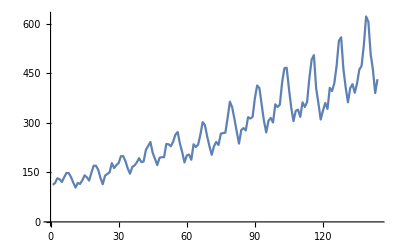

```mathematica
Clear[data]
data={112,118,132,129,121,135,148,148,136,119,104,118,115,126,141,135,125,149,170,170,158,133,114,140,145,150,178,163,172,178,199,199,184,162,146,166,171,180,193,181,183,218,230,242,209,191,172,194,196,196,236,235,229,243,264,272,237,211,180,201,204,188,235,227,234,264,302,293,259,229,203,229,242,233,267,269,270,315,364,347,312,274,237,278,284,277,317,313,318,374,413,405,355,306,271,306,315,301,356,348,355,422,465,467,404,347,305,336,340,318,362,348,363,435,491,505,404,359,310,337,360,342,406,396,420,472,548,559,463,407,362,405,417,391,419,461,472,535,622,606,508,461,390,432};
ListLinePlot@data
```

Применим параметрическое преобразование Бокса-Кокса для стабилизации дисперсии

```mathematica
Differences[]
```

```mathematica
Clear[λList,yList,logL,findMax,λ,boxCoxData]
λList=Range[-1,1,0.01];
yList={};
```

```mathematica
logL[λList_,yList_,data_]:=-(Length@data)/2*Log[Sum[(yList⟦i⟧-Mean@yList)^2,{i,Length@yList}]/(Length@data)]+(λList-1)*Sum[Log[data⟦i⟧],{i,Length@data}]
```

```mathematica
findMax[λList_,data_]:=Module[{maxL=-1000000,maxλ,yList},
Do[yList={};
Do[If[λList⟦j⟧≠0,AppendTo[yList,(data⟦i⟧^λList⟦j⟧-1)/λList⟦j⟧],AppendTo[yList,Log[data⟦i⟧]]],
{i,Length@data}];
If[Max[logL[λList,yList,data]]>maxL,maxL=Max[logL[λList,yList,data]];maxλ=λList⟦j⟧],
{j,Length@λList}];
{maxL,maxλ}]
```

```mathematica
findMax[λList,data]
```

{899.871,-1.}

```mathematica
λ=findMax[λList,data]⟦-1⟧;
```

```mathematica
boxCoxData=(#^λ-1)/λ&/@data
```

{0.991071,0.991525,0.992424,0.992248,0.991736,0.992593,0.993243,0.993243,0.992647,0.991597,0.990385,0.991525,0.991304,0.992063,0.992908,0.992593,0.992,0.993289,0.994118,0.994118,0.993671,0.992481,0.991228,0.992857,0.993103,0.993333,0.994382,0.993865,0.994186,0.994382,0.994975,0.994975,0.994565,0.993827,0.993151,0.993976,0.994152,0.994444,0.994819,0.994475,0.994536,0.995413,0.995652,0.995868,0.995215,0.994764,0.994186,0.994845,0.994898,0.994898,0.995763,0.995745,0.995633,0.995885,0.996212,0.996324,0.995781,0.995261,0.994444,0.995025,0.995098,0.994681,0.995745,0.995595,0.995726,0.996212,0.996689,0.996587,0.996139,0.995633,0.995074,0.995633,0.995868,0.995708,0.996255,0.996283,0.996296,0.996825,0.997253,0.997118,0.996795,0.99635,0.995781,0.996403,0.996479,0.99639,0.996845,0.996805,0.996855,0.997326,0.997579,0.997531,0.997183,0.996732,0.99631,0.996732,0.996825,0.996678,0.997191,0.997126,0.997183,0.99763,0.997849,0.997859,0.997525,0.997118,0.996721,0.997024,0.997059,0.996855,0.997238,0.997126,0.997245,0.997701,0.997963,0.99802,0.997525,0.997214,0.996774,0.997033,0.997222,0.997076,0.997537,0.997475,0.997619,0.997881,0.998175,0.998211,0.99784,0.997543,0.997238,0.997531,0.997602,0.997442,0.997613,0.997831,0.997881,0.998131,0.998392,0.99835,0.998031,0.997831,0.997436,0.997685}

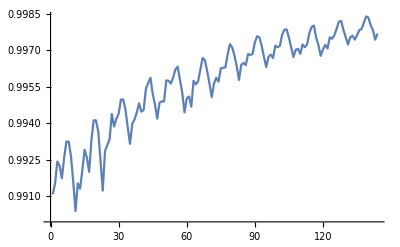

```mathematica
ListLinePlot@boxCoxData
```

Сезонное дифференцирование

Длина сезона S = 12 (определено по графику)

```mathematica
Clear[seasonDefData,s]
s=12;
seasonDefData=boxCoxData⟦;;s⟧;

Do[AppendTo[seasonDefData,boxCoxData⟦i⟧-boxCoxData⟦i-s⟧],{i,s+1,Length@boxCoxData}]
```

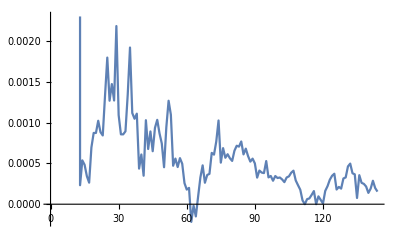

```mathematica
ListLinePlot@seasonDefData
```

Дифференцирование

```mathematica
Clear[defData]
```

```mathematica
defData={seasonDefData⟦1⟧};
Do[AppendTo[defData,seasonDefData⟦i⟧-seasonDefData⟦i-1⟧],{i,2,Length@seasonDefData}]
```

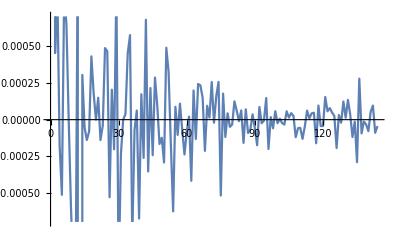

```mathematica
ListLinePlot@defData
```

```mathematica
UnitRootTest
```

Проверка стационарности

SARIMA(2,1,0),(1,1,0)

Следовательно, ряд необходимо продифференцировать и сезонно продифференцировать по 1 разу (готово).

```mathematica
column1=data⟦2;;-2⟧;
column2=data⟦;;-3⟧;
column3=ConstantArray[1,Length@data-2];
matrix={column1,column2,column3};
variables={fi1,fi2,α};
t=Length@data-2;
```